```mathematica
3+5
6*9
```

8

54

```mathematica
myList={1,2,3,4,5}
myList*5
```

{1,2,3,4,5}

{5,10,15,20,25}

```mathematica
NestList[#*2&,1,10]*35
```

{35,70,140,280,560,1120,2240,4480,8960,17920,35840}

```mathematica
myList=NestList[#*2&,3,1]
ListPlot[myList]
```

{3,6}

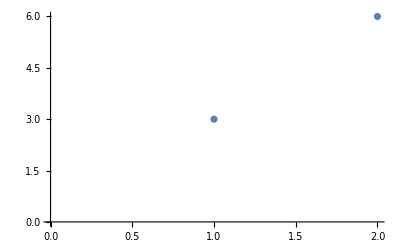

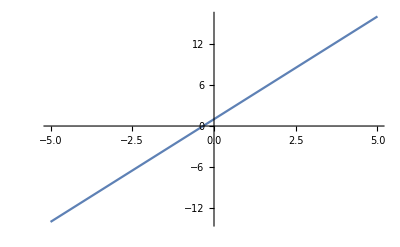

```mathematica
Plot[3x+1,{x,-5,5}]
```

```mathematica
Solve[x^2+2x-7==0,x]
N[%]
```

{{x→-1-2 √2},{x→-1+2 √2}}

{{x→-3.82843},{x→1.82843}}

```mathematica
Integrate[x^3+2x-3,x]
```

-3 x+x^2+x^4/4

```mathematica
Integrate[x^3+2x-3,{x,0,5}]
```

665/4

```mathematica
Plot[e^-Bx*sin(Wx),{x,0,B}]
```

Plot::plln: Limiting value B in {x,0,B} is not a machine-sized real number.

Plot[e^-Bx sin Wx,{x,0,B}]

```mathematica
Manipulate[Plot[Exp[-b x]*Sin[w x],{x,0,2Pi}],{b,0,2},{w,0,4}]
```